Input Parameter

```mathematica
(*gmW2= SetPrecision[8/(√2)GF,100];(*GF is Fermi constant, gmW2 is g^2/mW^2 where mW is mass of W boson, g is Electroweak SU(2) coupling*)
GF = SetPrecision[1.166378*10^-5,100]*)(*GeV^-2*)
(*Eps= 3/4;(*For valid solution in Universality condition*)*)
```

## Bounded Equation for New Scalar

```mathematica
(*Defined parameters used in Michel paramter*)
Clear[Rho,Eta,Eps,Yl,Yr,YR,YL,gmW2,GFSM]
aY[Yl_,YL_,Yr_,YR_]:=YL*Yr+YR*Yl;(*Ex: YL= (|YL|^2)/mV^2*)
AY[Yl_,YL_,Yr_,YR_]:=YL*Yr-YR*Yl;
bY[Yl_,YL_,Yr_,YR_]:=YR*Yr+YL*Yl+gmW2^2;
BY[Yl_,YL_,Yr_,YR_]:=YR*Yr-YL*Yl+gmW2^2;
cY[Yl_,YL_,Yr_,YR_]:=1/8*(YR*Yl+YL*Yr);
CY[Yl_,YL_,Yr_,YR_]:=1/8*(YR*Yl-YL*Yr);
(*Michel paramters for New Scalar*)
YBRho[Yl_,YL_,Yr_,YR_]:=3bY[Yl,YL,Yr,YR]+6cY[Yl,YL,Yr,YR]== Rho*(aY[Yl,YL,Yr,YR]+4bY[Yl,YL,Yr,YR]+6cY[Yl,YL,Yr,YR]);
YBEps[Yl_,YL_,Yr_,YR_]:=3BY[Yl,YL,Yr,YR]-6CY[Yl,YL,Yr,YR]== Eps*(-3AY[Yl,YL,Yr,YR]+4BY[Yl,YL,Yr,YR]-14CY[Yl,YL,Yr,YR]);
YBEta[Yl_,YL_,Yr_,YR_]:=-3AY[Yl,YL,Yr,YR]+4BY[Yl,YL,Yr,YR]-14CY[Yl,YL,Yr,YR]== Eta*(aY[Yl,YL,Yr,YR]+4bY[Yl,YL,Yr,YR]+6cY[Yl,YL,Yr,YR]);
YGF[Yl_,YL_,Yr_,YR_]:=(aY[Yl,YL,Yr,YR]+4bY[Yl,YL,Yr,YR]+6cY[Yl,YL,Yr,YR])== 128*GFSM^2;
```

```mathematica
Y = Flatten[Solve[{YBRho[Yl,YL,Yr,YR],YBEps[Yl,YL,Yr,YR],YBEta[Yl,YL,Yr,YR],YGF[Yl,YL,Yr,YR]},{YL,Yr,Yl,YR}],1]//Simplify
```

{}

```mathematica
(*Assume Universality of Y matrix*)
(*YR = Flatten[Solve[√(YRr*Evaluate[YLl/.Y[[1]]])==Evaluate[YLr/.Y[[2]]],YRr],1]//Simplify*)
```

```mathematica
YLl[Rho_,Eta_,Eps_,GFSM_]:=Evaluate[YLl/.Y]
YLr[Rho_,Eta_,Eps_,GFSM_]:=Evaluate[YLr/.Y]
YRr[Rho_,Eta_,Eps_,GFSM_]:=Evaluate[YRr/.Y]
YRl[Rho_,Eta_,Eps_,GFSM_]:=Evaluate[YRl/.Y]
```

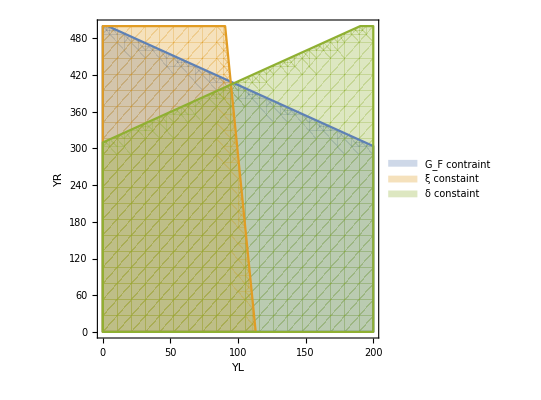

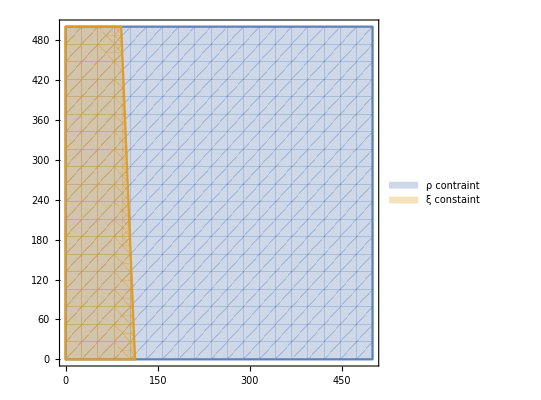

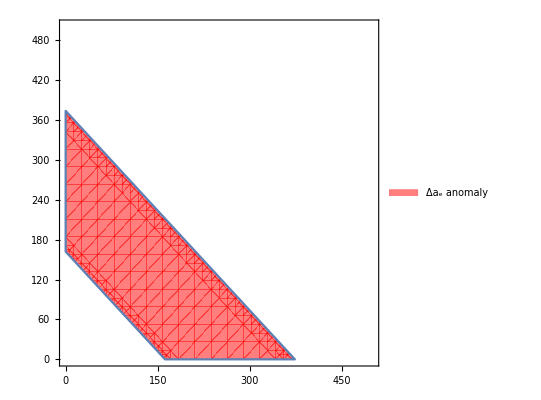

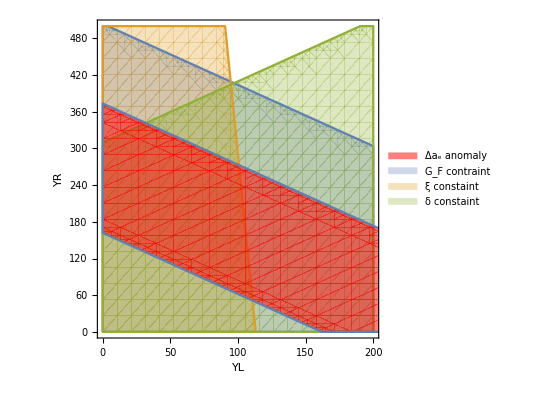

NonUniver.pdf

```mathematica
mμ=SetPrecision[0.00051099895,100];(*GeV*)
Clear[Coup]
Coup=6*10^-10;
YMDM[YL_,YR_,mc1_,m2_]:=((YL+YR) (m2^4-2 m2^2 mc1^2+(-2 m2^2 mc1^2+2 mc1^4) Log[mc1^2/(-m2^2+mc1^2)]))/(2 m2^4);
gmW2= SetPrecision[8/(√2)GF,100];(*GF is Fermi constant, gmW2 is g^2/mW^2 where mW is mass of W boson, g is Electroweak SU(2) coupling*)
GF = SetPrecision[1.1657*10^-5,100](*GeV^-2*);
GFSM=SetPrecision[1.1663787*10^-5,100](*GeV^-2*);
mV = SetPrecision[10,100];
O1 = RegionPlot[{128 GFSM^2-(aY[Coup,GF*x,Coup,GF*y]+4bY[Coup,GF*x,Coup,GF*y]+6cY[Coup,GF*x,Coup,GF*y])≥0 ,1.0041≥(-3AY[Coup,GF*x,Coup,GF*y]+4BY[Coup,GF*x,Coup,GF*y]-14CY[Coup,GF*x,Coup,GF*y])/(aY[Coup,GF*x,Coup,GF*y]+4bY[Coup,GF*x,Coup,GF*y]+6cY[Coup,GF*x,Coup,GF*y])≥0.9995,0.75115≥ (3BY[Coup,GF*x,Coup,GF*y]-6CY[Coup,GF*x,Coup,GF*y])/(-3AY[Coup,GF*x,Coup,GF*y]+4BY[Coup,GF*x,Coup,GF*y]-14CY[Coup,GF*x,Coup,GF*y])≥0.74979},{x,0,2*10^2},{y,0,5*10^2},FrameLabel->{"YL","YR"},PlotLegends->{"G_F contraint","ξ constaint","δ constaint"}]
RegionPlot[{0.75031
≥(3bY[Coup,GF*x,Coup,GF*y]+6cY[Coup,GF*x,Coup,GF*y])/(aY[Coup,GF*x,Coup,GF*y]+4bY[Coup,GF*x,Coup,GF*y]+6cY[Coup,GF*x,Coup,GF*y]) ≥0.74927,1.0041≥(-3AY[Coup,GF*x,Coup,GF*y]+4BY[Coup,GF*x,Coup,GF*y]-14CY[Coup,GF*x,Coup,GF*y])/(aY[Coup,GF*x,Coup,GF*y]+4bY[Coup,GF*x,Coup,GF*y]+6cY[Coup,GF*x,Coup,GF*y])≥0.9995},{x,0,5*10^2},{y,0,5*10^2},PlotLegends->{"ρ contraint","ξ constaint","δ constaint"}]
O2=RegionPlot[-1.2*10^-12≤  YMDM[x*GF*mV^2,y*GF*mV^2,mV,mμ]/(16*Pi^2)≤ -5.2*10^-13,{x,0,5*10^2},{y,0,5*10^2},PlotLegends->Placed[{"Δa_e anomaly"},{0.8,0.8}],PlotStyle->Opacity[0.5,Red]]
final = Show[O1,O2]
```

### Plotting

To have valid data for Universality coupling case, Eps =3/4 and (12+9Eta)/28≤ Rho ≤ 3/4.

```mathematica
(*ParametricPlot[{{Evaluate[YRl/.YU],Evaluate[YRr/.YU]},{Evaluate[YRl/.YL],Evaluate[YRr/.YL]}},{YLl,(0.05*4Pi)^2,(0.05*4Pi)^2/10^-12},PlotLegends->{"Upper bound","Lower bound"},ScalingFunctions->Automatic]*)
```

```mathematica
(*YLr[Rho_,Eps_,Eta_,YRr_]:=Evaluate[YLr/.Y]
YLl[Rho_,Eps_,Eta_,YRr_]:=Evaluate[YLl/.Y]
YRl[Rho_,Eps_,Eta_,YRr_]:=Evaluate[YRl/.Y]*)
```

```mathematica
(*Flatten[Table[If[YLr[Rho,Eps,Eta,YRr]≥-0.1&&YLr[Rho,Eps,Eta,YRr]≤ (4Pi)^2/10^-12&&YLl[Rho,Eps,Eta,YRr]≥-0.1&&YLl[Rho,Eps,Eta,YRr]≤ (4Pi)^2/10^-12&&YRl[Rho,Eps,Eta,YRr]≥-0.1&&YRl[Rho,Eps,Eta,YRr]≤ (4Pi)^2/10^-12,{YLr[Rho,Eps,Eta,YRr],YLl[Rho,Eps,Eta,YRr],YRl[Rho,Eps,Eta,YRr]},Null],{Rho,0.74979-0.00026,0.74979+0.00026,0.002},{Eps,0.75047-0.00034,0.75047+0.00034,0.0002},{Eta,1.0009-0.0007,1.0009+0.0016,0.0005},{YRr,0,10,1}],3];*)
```

```mathematica
(*ListPointPlot3D[Flatten[Table[If[YLr[Rho,Eps,Eta,YRr]≥-0.1&&YLr[Rho,Eps,Eta,YRr]≤ (4Pi)^2/10^-12&&YLl[Rho,Eps,Eta,YRr]≥-0.1&&YLl[Rho,Eps,Eta,YRr]≤ (4Pi)^2/10^-12&&YRl[Rho,Eps,Eta,YRr]≥-0.1&&YRl[Rho,Eps,Eta,YRr]≤ (4Pi)^2/10^-12,{YLr[Rho,Eps,Eta,YRr],YLl[Rho,Eps,Eta,YRr],YRl[Rho,Eps,Eta,YRr]},Null],{Rho,0.74979-0.00026,0.74979+0.00026,0.002},{Eps,0.75047-0.00034,0.75047+0.00034,0.0002},{Eta,1.0009-0.0007,1.0009+0.0016,0.0005},{YRr,0,10,1}],3],AxesLabel->{"YLr","YLl","YRl"}]*)
```

```mathematica
YLl[Rho_,Eta_,YRr_]:=Evaluate[YLl/.Y]
YLr[Rho_,Eta_,YRr_]:=Evaluate[YLr/.Y]
YRr[Rho_,Eta_]:=Evaluate[YRr/.YR[[2]]]
YLl[Rho_,Eta_]:=YLl[Rho,Eta,YRr[Rho,Eta]]
```

```mathematica
gmW2= SetPrecision[8/(√2)GF,100];(*GF is Fermi constant, gmW2 is g^2/mW^2 where mW is mass of W boson, g is Electroweak SU(2) coupling*)
GF = SetPrecision[1.1657*10^-5,100](*GeV^-2*);
GFSM=SetPrecision[1.1663787*10^-5,100](*GeV^-2*);
Data = Flatten[Table[If[YLl[Rho,Eta]≥0&&YRr[Rho,Eta]≥0,{YLl[Rho,Eta],YRr[Rho,Eta]},Null],{Rho,0.74979-0.00052,0.74979+0.00052,0.00001},{Eta,1.0009-0.0014,1.0009+0.0032,0.0001}],1];
Data0 = Table[{0,i}, {i,0,10^-9,10^-11}];
```

Power::infy: Infinite expression 1/0. encountered.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

Power::infy: Infinite expression 1/0. encountered.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

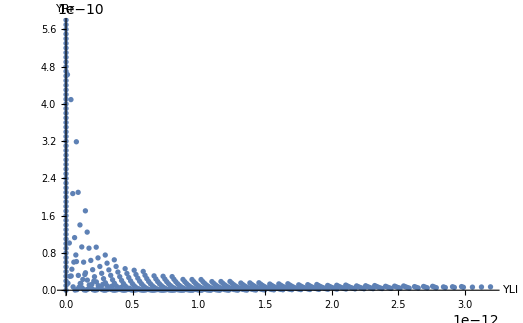

```mathematica
ListPlot[Flatten[{Data,Data0},1],AxesLabel->{"YLl","YRr"}]
```

```mathematica
(*Manipulate[ListPointPlot3D[Flatten[Table[{YLr[Rho,Eps,Eta,YRr],YLl[Rho,Eps,Eta,YRr],YRl[Rho,Eps,Eta,YRr]},{Rho,0.74979-0.00026,0.74979+0.00026,0.002},{Eps,0.75047-0.00034,0.75047+0.00034,0.0002},{Eta,1.0009-0.0007,1.0009+0.0016,0.0005}],2],PlotRange->{{-0.00001,0.00001},{-0.00001,0.00001},{-0.00001,0.00001}},PlotStyle->PointSize[Large]],{YRr,0,1, 0.01}]*)
```

## Bounded Equation for New Vector

```mathematica
(*Defined parameters used in Michel paramter*)
Clear[Vl,VL,Vr,VR,ReVRr,Rho,Eta,gmW2,GFSM]
aV[Vl_,VL_,Vr_,VR_]:=VL*Vr^2+VR^2*Vl;(*Ex: VL = (|VL|^2)/mV^2*)
AV[Vl_,VL_,Vr_,VR_]:=VL*Vr^2-VR^2*Vl;
bV[Vl_,VL_,Vr_,VR_,cthe_]:=4*(VR^2*Vr^2+VL*Vl)+gmW2^2+4*gmW2*VR*Vr*cthe ;(*ReVRr = (Re(VR x Vr^*))/mV^2=(|VR|*|Vr|)/mV^2*cosθ*)
BV[Vl_,VL_,Vr_,VR_,cthe_]:=4*(VR^2*Vr^2-VL*Vl)+gmW2^2+4*gmW2*VR*Vr*cthe;
(*Michel paramters for New Vector*)
VBRho[Vl_,VL_,Vr_,VR_,cthe_]:=(3bV[Vl,VL,Vr,VR,cthe])/(aV[Vl,VL,Vr,VR]+4bV[Vl,VL,Vr,VR,cthe])==Rho;
VBEps[Vl_,VL_,Vr_,VR_,cthe_]:=(3BV[Vl,VL,Vr,VR,cthe])/(-3AV[Vl,VL,Vr,VR]+4BV[Vl,VL,Vr,VR,cthe])==Eps;
VBEta[Vl_,VL_,Vr_,VR_,cthe_]:=(-3AV[Vl,VL,Vr,VR]+4BV[Vl,VL,Vr,VR,cthe])/(aV[Vl,VL,Vr,VR]+4bV[Vl,VL,Vr,VR,cthe])==Eta;
VGF[Vl_,VL_,Vr_,VR_,cthe_]:=aV[Vl,VL,Vr,VR]+4bV[Vl,VL,Vr,VR,cthe]== 128*GFSM^2;
```

```mathematica
(*VRr:=ReVRr^2;(*Assume V matrix is real*)*)
V= Flatten[Solve[{VBRho[Vl,VL,Vr,VR,cthe],VBEps[Vl,VL,Vr,VR,cthe],VBEta[Vl,VL,Vr,VR,cthe],VGF[Vl,VL,Vr,VR,cthe]},{VL,Vr,VR,Vl}],1]//Simplify
```

{}

```mathematica
(*Assume Universality of V matrix*)
(*VR = Flatten[Solve[√(VRr*Evaluate[VLl/.V[[1]]])==Evaluate[VLr/.V[[2]]],VRr],1]//Simplify*)
```

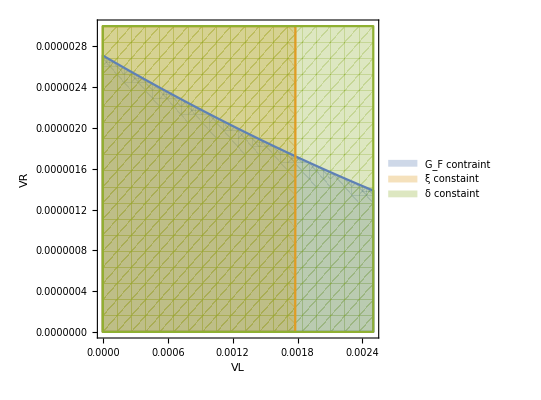

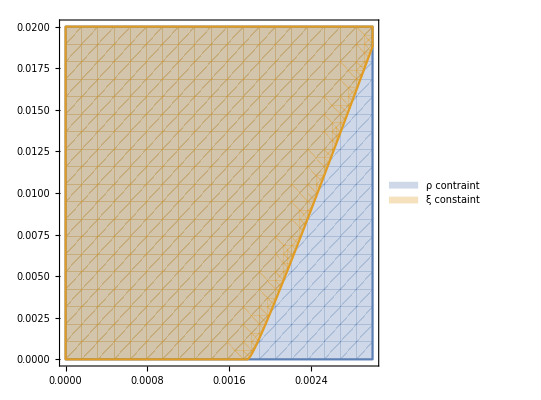

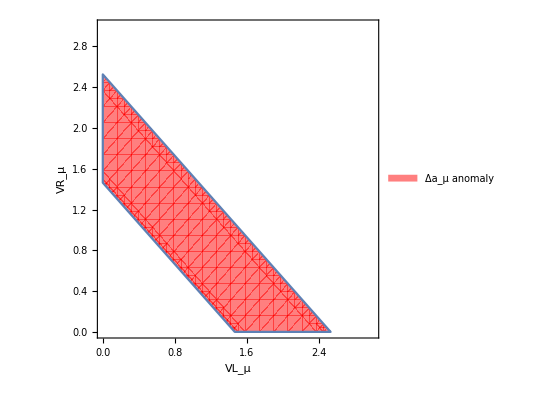

-Graphics-

-Graphics-

NonUniver-vector-muonMDM_cos1.pdf

```mathematica
mμ=SetPrecision[0.1056583755,100]; (*GeV*)
Clear[cthe,Coup]
cthe= 1;
Coup = GF ;
VMDM[VL_,VR_,mW_,m2_]:=((VL+VR) (m2^6+8 m2^4 mW^2-4 m2^2 mW^4+2 (3 m2^4 mW^2-5 m2^2 mW^4+2 mW^6) Log[mW^2/(-m2^2+mW^2)]))/(2 m2^4 mW^2)
gmW2= SetPrecision[8/(√2)GF,100];(*GF is Fermi constant, gmW2 is g^2/mW^2 where mW is mass of W boson, g is Electroweak SU(2) coupling*)
GF = SetPrecision[1.1657*10^-5,100](*GeV^-2*);
GFSM=SetPrecision[1.1663787*10^-5,100](*GeV^-2*);
mV = SetPrecision[10,100];
VO1 =RegionPlot[{128 GFSM^2-(aV[Coup,GF*x,√Coup,√(GF*y)]+4bV[Coup,GF*x,√Coup,√(GF*y),cthe])≥0 ,1.0041≥(-3AV[Coup,GF*x,√Coup,√(GF*y)]+4BV[Coup,GF*x,√Coup,√(GF*y),cthe])/(aV[Coup,GF*x,√Coup,√(GF*y)]+4bV[Coup,GF*x,√Coup,√(GF*y),cthe])≥0.9995,0.75115≥ (3BV[Coup,GF*x,√Coup,√(GF*y),cthe])/(-3AV[Coup,GF*x,√Coup,√(GF*y)]+4BV[Coup,GF*x,√Coup,√(GF*y),cthe])≥0.74979},{x,0,0.0025},{y,0,0.000003},FrameLabel->{"VL","VR"},PlotLegends->{"G_F contraint","ξ constaint","δ constaint"}]
RegionPlot[{0.75031
≥(3bV[Coup,GF*x,√Coup,√(GF*y),cthe])/(aV[Coup,GF*x,√Coup,√(GF*y)]+4bV[Coup,GF*x,√Coup,√(GF*y),cthe]) ≥0.74927,1.0041≥(-3AV[Coup,GF*x,√Coup,√(GF*y)]+4BV[Coup,GF*x,√Coup,√(GF*y),cthe])/(aV[Coup,GF*x,√Coup,√(GF*y)]+4bV[Coup,GF*x,√Coup,√(GF*y),cthe])≥0.9995},{x,0,0.003},{y,0,0.02},PlotLegends->{"ρ contraint","ξ constaint","δ constaint"}]
VO2=RegionPlot[2.01*10^-9≤  VMDM[x*GF*mV^2,y*GF*mV^2,mV,mμ]/(16*Pi^2)≤ 3.47*10^-9,{x,0,3},{y,0,3},PlotLegends->Placed[{"Δa_μ anomaly"},{0.8,0.8}],PlotStyle->Opacity[0.5,Red],FrameLabel->{"VL_μ","VR_μ"}]
VO3=ListPlot[{{1,1}},PlotStyle->{Directive[Yellow,PointSize[0.05]]},Frame->True,PlotLabels->"[1,1]"]
final = Show[VO2,VO3]
Export["NonUniver-vector-muonMDM_cos1.pdf",VO1 ]
```

### Plotting

```mathematica
VLr[Rho_,Eta_,ReVRr_,VRr_]:=Evaluate[VLr/.V]
VLl[Rho_,Eta_,ReVRr_,VRr_]:=Evaluate[VLl/.V]
VRr[Rho_,Eta_,ReVRr_]:=Evaluate[VRr/.VR[[2]]]
VLl[Rho_,Eta_,ReVRr_]:=VLl[Rho,Eta,ReVRr,VRr[Rho,Eta,ReVRr]]
```

```mathematica
(*ListPointPlot3D[Flatten[Table[If[VLr[Rho,Eps,Eta,ReVRr]≥-0.00001&&VLr[Rho,Eps,Eta,ReVRr]≤ (4Pi)^2/10^-12&&VLl[Rho,Eps,Eta,ReVRr]≥-0.00001&&VLl[Rho,Eps,Eta,ReVRr]≤ (4Pi)^2/10^-12&&VRl[Rho,Eps,Eta,ReVRr]≥-0.00001&&VRl[Rho,Eps,Eta,ReVRr]≤ (4Pi)^2/10^-12,{VLr[Rho,Eps,Eta,ReVRr],VLl[Rho,Eps,Eta,ReVRr],VRl[Rho,Eps,Eta,ReVRr]},Null],{Rho,0.74979-0.00026,0.74979+0.00026,0.002},{Eps,0.75047-0.00034,0.75047+0.00034,0.0002},{Eta,1.0009-0.0007,1.0009+0.0016,0.0005},{ReVRr,-100,100,1}],3],AxesLabel->{"VLr","VLl","VRl"}]*)
```

```mathematica
gmW2= SetPrecision[8/(√2)GF,100];(*GF is Fermi constant, gmW2 is g^2/mW^2 where mW is mass of W boson, g is Electroweak SU(2) coupling*)
GF = SetPrecision[1.166378*10^-5,100](*GeV^-2*);
data= Flatten[Table[If[VLl[Rho,Eta,ReVRr]≥0&&VRr[Rho,Eta,ReVRr]≥0&&VLr[Rho,Eta,ReVRr,VRr[Rho,Eta,ReVRr]]≥ 0,{VLl[Rho,Eta,ReVRr],VRr[Rho,Eta,ReVRr]},Null],{Rho,0.74979-0.00052,0.74979+0.00052,0.00001},{Eta,1.0009-0.0014,1.0009+0.0032,0.0001},{ReVRr,-10,10,1}],2];
```

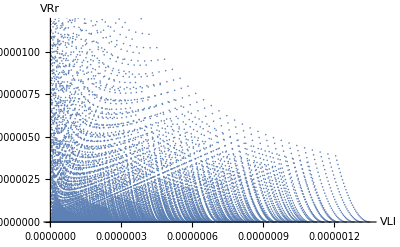

```mathematica
ListPlot[data,AxesLabel->{"VLl","VRr"}]
```

## Bounded Equation for New Vector only couples to Muon

```mathematica
(*Defined parameters used in Michel paramter*)
Clear[Vl,Vr,Rho,Eta,gmW2,GFSM,mμ,mV]
aV[Vl_,Vr_]:=(mμ/(4*Pi))^4*gmW2^2*Vl*Vr;(*Ex: Vl = (|Vl|^2)/mV^2*)
AV[Vl_,Vr_]:=-(mμ/(4*Pi))^4*gmW2^2*Vl*Vr;
bV[Vl_,Vr_]:=(mμ/Pi)^4*(gmW2^2*Vr^2)/2^10+gmW2^2/16-(mμ/(8*Pi))^2*gmW2^2*Vr;
BV[Vl_,Vr_]:=(mμ/Pi)^4*(gmW2^2*Vr^2)/2^10+gmW2^2/16-(mμ/(8*Pi))^2*gmW2^2*Vr;
(*Michel paramters for New Vector*)
VBRho[Vl_,Vr_]:=(3bV[Vl,Vr])/(aV[Vl,Vr]+4bV[Vl,Vr])==Rho;
VBEps[Vl_,Vr_]:=(3BV[Vl,Vr])/(-3AV[Vl,Vr]+4BV[Vl,Vr])==Eps;
VBEta[Vl_,Vr_]:=(-3AV[Vl,Vr]+4BV[Vl,Vr])/(aV[Vl,Vr]+4bV[Vl,Vr])==Eta;
VGF[Vl_,Vr_]:=aV[Vl,Vr]+4bV[Vl,Vr]== 128*GFSM^2;
```

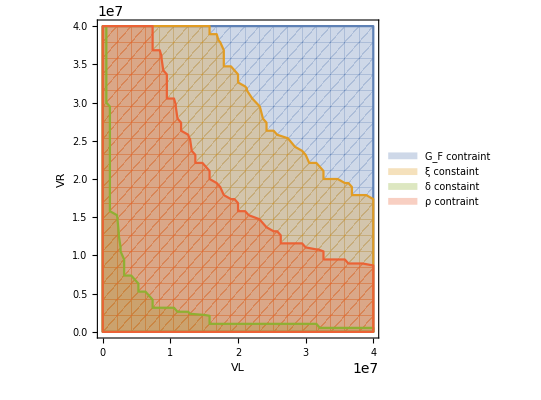

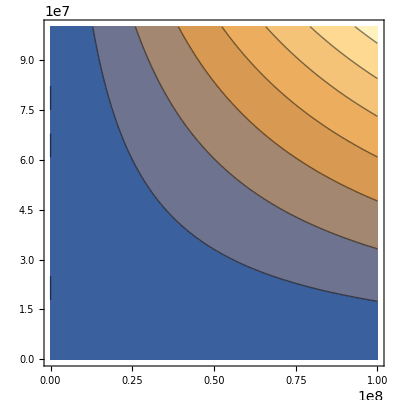

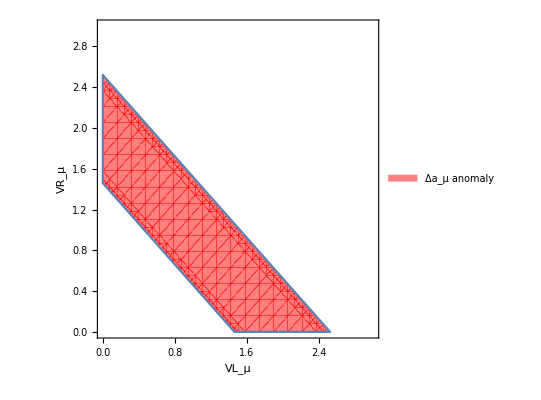

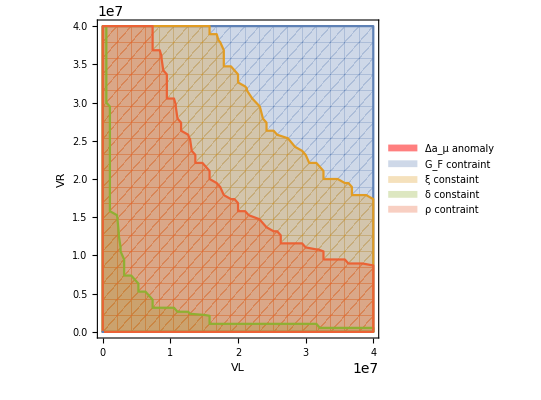

```mathematica
mμ=SetPrecision[0.1056583755,100]; (*GeV*)
VMDM[VL_,VR_,mW_,m2_]:=((VL+VR) (m2^6+8 m2^4 mW^2-4 m2^2 mW^4+2 (3 m2^4 mW^2-5 m2^2 mW^4+2 mW^6) Log[mW^2/(-m2^2+mW^2)]))/(2 m2^4 mW^2)
gmW2= SetPrecision[8/(√2)GF,100];(*GF is Fermi constant, gmW2 is g^2/mW^2 where mW is mass of W boson, g is Electroweak SU(2) coupling*)
GF = SetPrecision[1.1657*10^-5,100](*GeV^-2*);
GFSM=SetPrecision[1.1663787*10^-5,100](*GeV^-2*);
mV = SetPrecision[1,100];
VO1 =RegionPlot[{128 GFSM^2-(aV[GF*x,GF*y]+4bV[GF*x,GF*y])≥0 ,1.0041≥(-3AV[GF*x,GF*y]+4BV[GF*x,GF*y])/(aV[GF*x,GF*y]+4bV[GF*x,GF*y])≥0.9995,0.75115≥ (3BV[GF*x,GF*y])/(-3AV[GF*x,GF*y]+4BV[GF*x,GF*y])≥0.74979,0.75031
≥(3bV[GF*x,GF*y])/(aV[GF*x,GF*y]+4bV[GF*x,GF*y]) ≥0.74927},{x,0,4*10^7},{y,0,4*10^7},FrameLabel->{"VL","VR"},PlotLegends->{"G_F contraint","ξ constaint","δ constaint","ρ contraint"}]
ContourPlot[{(-3AV[GF*x,GF*y]+4BV[GF*x,GF*y])/(aV[GF*x,GF*y]+4bV[GF*x,GF*y])},{x,0,10^8},{y,0,10^8},PlotLegends->{"ρ contraint","ξ constaint","δ constaint"}]
VO=RegionPlot[2.01*10^-9≤  VMDM[x*GF*mV^2,y*GF*mV^2,mV,mμ]/(16*Pi^2)≤ 3.47*10^-9,{x,0,3},{y,0,3},PlotLegends->Placed[{"Δa_μ anomaly"},{0.8,0.8}],PlotStyle->Opacity[0.5,Red],FrameLabel->{"VL_μ","VR_μ"}]
final = Show[VO1,VO]
(*Export["vector_couple_muon-muonMDM.pdf",final]*)
```